```mathematica
1+1
```

2

```mathematica
Clear[k]
Clear[x]
Clear[λ]
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*Hypergeometric1F1[2+1,1,-(σ*k^2)/2],k,x]
```

```mathematica
1/(2 √(2 π))(-(4 (λ^4-4 λ^3 σ-7 x^2 λ σ^2+2 x^2 (x^2-σ) σ^2+4 λ^2 σ (x^2+σ)))/(λ-2 σ)^5+(4 x (-2 λ^4+4 λ^2 (-2 x^2+λ) σ+(-4 x^4+12 x^2 λ+9 λ^2) σ^2+4 (2 x^2-5 λ) σ^3+4 σ^4) DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(11/2))
```

```mathematica
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*k^2*Hypergeometric1F1[1+2,1+2,-(σ*k^2)/2],k,x]
```

```mathematica
1/((λ-2 σ)^3 √(-λ+2 σ))4 √(2/π) (x^2 √(-λ+2 σ)+λ √(-λ+2 σ)-2 σ √(-λ+2 σ)-2 x^3 DawsonF[x/(√(-λ+2 σ))]-3 x λ DawsonF[x/(√(-λ+2 σ))]+6 x σ DawsonF[x/(√(-λ+2 σ))])
```

```mathematica
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*Hypergeometric1F1[1,1,-(σ*k^2)/2],k,x]
```

```mathematica
(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π))
```

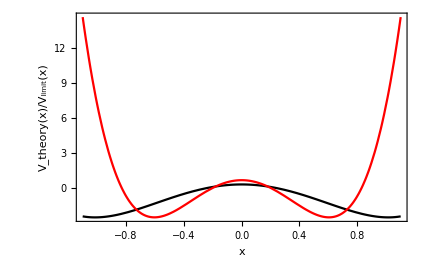

```mathematica
Vthe[x_,τ_,α0_,λ_,n_,γ_]:=(
σ=λ/(1-Exp[-2γ]);
result=√(2 π)*π*(2λ)/(1-Exp[-2γ])*1/(2π)*1/Abs[α0*Exp[γ]]^4*
(( 1/(1-Exp[-2γ]))^2* Gamma[2+1] *(-(4 (λ^4-4 λ^3 σ-7 x^2 λ σ^2+2 x^2 (x^2-σ) σ^2+4 λ^2 σ (x^2+σ)))/(λ-2 σ)^5+(4 x (-2 λ^4+4 λ^2 (-2 x^2+λ) σ+(-4 x^4+12 x^2 λ+9 λ^2) σ^2+4 (2 x^2-5 λ) σ^3+4 σ^4) DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(11/2))/(2 √(2 π))
÷
+0*Abs[α0*Exp[γ]]^4*(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π)));
Return[result+1/λ^2*1/Abs[α0]^4*2 λ^2*(1/2 - 1/(1-Exp[-2γ])  )*Re[α0^2*ⅇ^(-ⅈ *2τ)]]
);

Plot[{DawsonF[x]/x},{x,0,0.1},Frame->True,FrameLabel->{Style["x",20,Bold],Style["DawsonF(x)/x",20,Bold]},PlotRange->{0,2}];

(*Vlimit[x_,τ_,α0_,λ_,n_,γ_]:=1/λ^2*1/Abs[α0]^4*
 (6 x^4-17λ x^2  -λ*α0^2*ⅇ^(-ⅈ *2τ)*2 x^2 -λ*Conjugate[α0]^2*ⅇ^(ⅈ *2τ)*2 x^2 -λ*α0^2*ⅇ^(-ⅈ *2τ)*(λ/2 - λ/(1-Exp[-2γ])  )-λ*Conjugate[α0]^2*ⅇ^(ⅈ *2τ)*(λ/2 -λ/(1-Exp[-2γ])  )+4 λ^2+Abs[α0]^4);*)

Vlimit[x_,τ_,α0_,λ_,n_,γ_]:=1/λ^2*1/Abs[α0]^4*
 (6 x^4-17λ x^2  -4λ*x^2 Re[α0^2*ⅇ^(-ⅈ *2τ) ]-2 λ^2*(1/2 - 1/(1-Exp[-2γ])  )*Re[α0^2*ⅇ^(-ⅈ *2τ)]+ 4 λ^2+0*Abs[α0]^4)+1/λ^2*1/Abs[α0]^4*2 λ^2*(1/2 - 1/(1-Exp[-2γ])  )*Re[α0^2*ⅇ^(-ⅈ *2τ)];

n=2;
r=1.1*Abs[α0*Exp[γ]]*√(2λ);
γ=10^(-10);
τ=2π*3/(13n);
λ=0.2;
α0=1.0*Exp[I*2π*2/10]*1/(√(2λ));
Plot[{Vthe[x,τ,α0,λ,n,γ],Vlimit[x,τ,α0,λ,n,γ]},{x,-r,r},PlotStyle->{Black,Red},PlotRange->All,Frame->True,FrameLabel->{Style["x",20,Bold],Style["V_theory(x)/V_limit(x)",20,Bold]}]
```

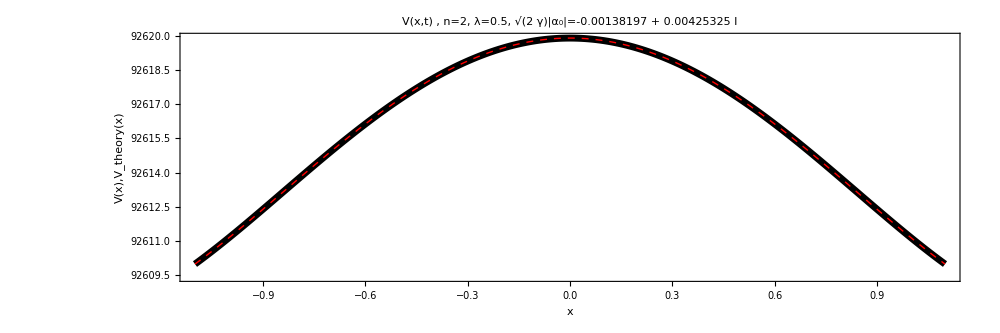

```mathematica
r=1.1*Abs[α0*Exp[γ]]*√(2λ);
ProgressIndicator[Dynamic[x],{-r,r}]
(*τ=2π*0.25;*)
τ=2π*7/(13n);
Vxlist1=Table[{x,Re[V[x,τ,α0,λ,n,γ]]},{x,-r,r,r/100}];
Vxlist2=Table[{x,Re[Vthe[x,τ,α0,λ,n,γ]]},{x,-r,r,r/100}];

ListLinePlot[{Vxlist1,Vxlist2},PlotRange->All,ImageSize->1000,Frame->True,FrameLabel->{Style["x",30,Bold],Style["V(x),V_theory(x)",30,Bold]},PlotLabel->Style[" V(x,t) "<>", n="<>ToString[n]<>", λ="<>ToString[λ]<>", √(2  γ)|α_0|="<>ToString[√(2γ)*α0]<>"\n",20],PlotRange->All,Axes->False,FrameStyle->Directive[Black,Thickness[0.003],30],PlotStyle->{Directive[Thickness[0.005],Black],Directive[Red,Dashed,Thick],Directive[Thickness[0.005],Blue]},AspectRatio->1/3 ]
```

```mathematica
Analytical expression of V(x,t) for n=3
```

```mathematica
Clear[k]
Clear[x]
Clear[λ]
Clear[σ]
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*Hypergeometric1F1[3+1,1,-(σ*k^2)/2],k,x]
```

1/(3 (-λ+2 σ)^(15/2))√(2/π) (√(-λ+2 σ) (3 λ^6-18 λ^5 σ+18 λ^4 σ (x^2+2 σ)+16 x^2 λ σ^3 (-2 x^2+3 σ)-3 λ^3 σ^2 (21 x^2+8 σ)+3 x^2 λ^2 σ^2 (6 x^2+11 σ)+4 x^2 σ^3 (x^4-2 x^2 σ-3 σ^2))+x (-6 λ^6+18 λ^5 σ-9 λ^4 (4 x^2-5 σ) σ+9 λ^3 (12 x^2-25 σ) σ^2-12 λ σ^3 (-5 x^4+14 x^2 σ+9 σ^2)+6 λ^2 σ^2 (-6 x^4+x^2 σ+45 σ^2)+8 σ^3 (-x^6+3 x^4 σ+3 x^2 σ^2+3 σ^3)) DawsonF[x/(√(-λ+2 σ))])

```mathematica
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*k^3*Hypergeometric1F1[1+3,1+3,-(σ*k^2)/2],k,x]
```

1/((λ-2 σ)^4 √(-λ+2 σ))4 ⅈ √(2/π) (-2 x^3 √(-λ+2 σ)-5 x λ √(-λ+2 σ)+10 x σ √(-λ+2 σ)+4 x^4 DawsonF[x/(√(-λ+2 σ))]+12 x^2 λ DawsonF[x/(√(-λ+2 σ))]+3 λ^2 DawsonF[x/(√(-λ+2 σ))]-24 x^2 σ DawsonF[x/(√(-λ+2 σ))]-12 λ σ DawsonF[x/(√(-λ+2 σ))]+12 σ^2 DawsonF[x/(√(-λ+2 σ))])

```mathematica
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*Hypergeometric1F1[1,1,-(σ*k^2)/2],k,x]
```

(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π))

```mathematica
Clear[k]
Clear[x]
Clear[λ]
Clear[σ]
FourierTransform[1/2*Abs[k]*Exp[λ/4 k^2]*Hypergeometric1F1[1,1,-(σ*k^2)/2],k,x]
```

(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π))

```mathematica
fT[k_,τ_,α0_,λ_,n_,γ_]:=λ/(1-Exp[-2γ])*1/Abs[α0*Exp[γ]]^(2n)*Exp[λ/4 k^2]*
  (( 1/(1-Exp[-2γ]))^n* Gamma[n+1] *Hypergeometric1F1[n+1,1,-k^2/2*λ/(1-Exp[-2γ])]-   ((-ⅈ*2^-1 *α0*Exp[γ]*√(2λ)*k*ⅇ^(-ⅈ *τ))/(1-Exp[-2γ]))^n* Hypergeometric1F1[1+n,1+n,-k^2/2*λ/(1-Exp[-2γ])]- ((-ⅈ*2^-1 *Conjugate[α0*Exp[γ]]*√(2λ)*k*ⅇ^(ⅈ *τ))/(1-Exp[-2γ]))^(n)*  Hypergeometric1F1[1+n,1+n,-k^2/2*λ/(1-Exp[-2γ])]+
Abs[α0*Exp[γ]]^(2n)* Hypergeometric1F1[1,1,-k^2/2*λ/(1-Exp[-2γ])]);
```

```mathematica
Vthe[x_,τ_,α0_,λ_,n_,γ_]:=(
σ=λ/(1-Exp[-2γ]);
result=√(2 π)*λ/(1-Exp[-2γ])*1/Abs[α0*Exp[γ]]^6*
(( 1/(1-Exp[-2γ]))^3* Gamma[3+1] *1/(3 (-λ+2 σ)^(15/2))√(2/π) (√(-λ+2 σ) (3 λ^6-18 λ^5 σ+18 λ^4 σ (x^2+2 σ)+16 x^2 λ σ^3 (-2 x^2+3 σ)-3 λ^3 σ^2 (21 x^2+8 σ)+3 x^2 λ^2 σ^2 (6 x^2+11 σ)+4 x^2 σ^3 (x^4-2 x^2 σ-3 σ^2))+x (-6 λ^6+18 λ^5 σ-9 λ^4 (4 x^2-5 σ) σ+9 λ^3 (12 x^2-25 σ) σ^2-12 λ σ^3 (-5 x^4+14 x^2 σ+9 σ^2)+6 λ^2 σ^2 (-6 x^4+x^2 σ+45 σ^2)+8 σ^3 (-x^6+3 x^4 σ+3 x^2 σ^2+3 σ^3)) DawsonF[x/(√(-λ+2 σ))])
-((-ⅈ*2^-1 *α0*Exp[γ]*√(2λ)*ⅇ^(-ⅈ *τ))/(1-Exp[-2γ]))^3*1/((λ-2 σ)^4 √(-λ+2 σ))4 ⅈ √(2/π) (-2 x^3 √(-λ+2 σ)-5 x λ √(-λ+2 σ)+10 x σ √(-λ+2 σ)+4 x^4 DawsonF[x/(√(-λ+2 σ))]+12 x^2 λ DawsonF[x/(√(-λ+2 σ))]+3 λ^2 DawsonF[x/(√(-λ+2 σ))]-24 x^2 σ DawsonF[x/(√(-λ+2 σ))]-12 λ σ DawsonF[x/(√(-λ+2 σ))]+12 σ^2 DawsonF[x/(√(-λ+2 σ))])
-((-ⅈ*2^-1 *Conjugate[α0*Exp[γ]]*√(2λ)*ⅇ^(ⅈ *τ))/(1-Exp[-2γ]))^3*1/((λ-2 σ)^4 √(-λ+2 σ))4 ⅈ √(2/π) (-2 x^3 √(-λ+2 σ)-5 x λ √(-λ+2 σ)+10 x σ √(-λ+2 σ)+4 x^4 DawsonF[x/(√(-λ+2 σ))]+12 x^2 λ DawsonF[x/(√(-λ+2 σ))]+3 λ^2 DawsonF[x/(√(-λ+2 σ))]-24 x^2 σ DawsonF[x/(√(-λ+2 σ))]-12 λ σ DawsonF[x/(√(-λ+2 σ))]+12 σ^2 DawsonF[x/(√(-λ+2 σ))])
+Abs[α0*Exp[γ]]^6*(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π)));
Return[result]
);

Vlimit[x_,τ_,α0_,λ_,n_,γ_]:=(
σ=λ/(1-Exp[-2γ]);
result=√(2 π)*1/Abs[α0*Exp[γ]]^6*
(( σ/λ)^3*6 *σ/(3 (-λ+2 σ)^(15/2))√(2/π) (√(-λ+2 σ) (3 λ^6-18 λ^5 σ+18 λ^4 σ (x^2+2 σ)+16 x^2 λ σ^3 (-2 x^2+3 σ)-3 λ^3 σ^2 (21 x^2+8 σ)+3 x^2 λ^2 σ^2 (6 x^2+11 σ)+4 x^2 σ^3 (x^4-2 x^2 σ-3 σ^2))+x (-6 λ^6+18 λ^5 σ-9 λ^4 (4 x^2-5 σ) σ+9 λ^3 (12 x^2-25 σ) σ^2-12 λ σ^3 (-5 x^4+14 x^2 σ+9 σ^2)+6 λ^2 σ^2 (-6 x^4+x^2 σ+45 σ^2)+8 σ^3 (-x^6+3 x^4 σ+3 x^2 σ^2+3 σ^3)) DawsonF[x/(√(-λ+2 σ))])
-((-ⅈ*2^-1 *α0*Exp[γ]*√(2λ)*ⅇ^(-ⅈ *τ))/(1-Exp[-2γ]))^3*σ/((λ-2 σ)^4 √(-λ+2 σ))4 ⅈ √(2/π) (-2 x^3 √(-λ+2 σ)-5 x λ √(-λ+2 σ)+10 x σ √(-λ+2 σ)+4 x^4 DawsonF[x/(√(-λ+2 σ))]+12 x^2 λ DawsonF[x/(√(-λ+2 σ))]+3 λ^2 DawsonF[x/(√(-λ+2 σ))]-24 x^2 σ DawsonF[x/(√(-λ+2 σ))]-12 λ σ DawsonF[x/(√(-λ+2 σ))]+12 σ^2 DawsonF[x/(√(-λ+2 σ))])
-((-ⅈ*2^-1 *Conjugate[α0*Exp[γ]]*√(2λ)*ⅇ^(ⅈ *τ))/(1-Exp[-2γ]))^3*σ/((λ-2 σ)^4 √(-λ+2 σ))4 ⅈ √(2/π) (-2 x^3 √(-λ+2 σ)-5 x λ √(-λ+2 σ)+10 x σ √(-λ+2 σ)+4 x^4 DawsonF[x/(√(-λ+2 σ))]+12 x^2 λ DawsonF[x/(√(-λ+2 σ))]+3 λ^2 DawsonF[x/(√(-λ+2 σ))]-24 x^2 σ DawsonF[x/(√(-λ+2 σ))]-12 λ σ DawsonF[x/(√(-λ+2 σ))]+12 σ^2 DawsonF[x/(√(-λ+2 σ))])
+σ*Abs[α0*Exp[γ]]^6*(-4/(λ-2 σ)-(8 x DawsonF[x/(√(-λ+2 σ))])/(-λ+2 σ)^(3/2))/(2 √(2 π)));
Return[result]
);
```

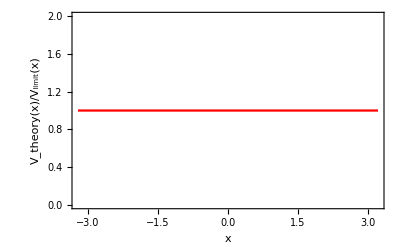

```mathematica
r=3.1*Abs[α0*Exp[γ]]*√(2λ);
γ=10^(-5);
τ=2π*3/(13n);
λ=0.5;
α0=1.0*Exp[I*2π*3/10]*1/(√(2λ));
Plot[{Vthe[x,τ,α0,λ,n,γ]/Vlimit[x,τ,α0,λ,n,γ]},{x,-r,r},PlotStyle->{Black,Red},PlotRange->{0,2},Frame->True,FrameLabel->{Style["x",20,Bold],Style["V_theory(x)/V_limit(x)",20,Bold]}]
```

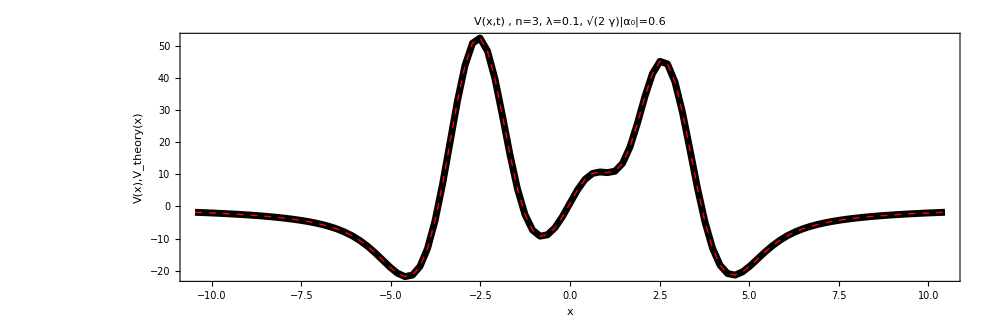

```mathematica
r=10.1*Abs[α0*Exp[γ]]*√(2λ);
ProgressIndicator[Dynamic[x],{-r,r}]
(*τ=2π*0.25;*)
τ=2π*1/(13n);
Vxlist1=Table[{x,Re[V[x,τ,α0,λ,n,γ]]},{x,-r,r,r/50}];
Vxlist2=Table[{x,Re[Vthe[x,τ,α0,λ,n,γ]]},{x,-r,r,r/50}];

ListLinePlot[{Vxlist1,Vxlist2},PlotRange->All,ImageSize->1000,Frame->True,FrameLabel->{Style["x",30,Bold],Style["V(x),V_theory(x)",30,Bold]},PlotLabel->Style[" V(x,t) "<>", n="<>ToString[n]<>", λ="<>ToString[λ]<>", √(2  γ)|α_0|="<>ToString[√(2γ)*α0]<>"\n",20],PlotRange->All,Axes->False,FrameStyle->Directive[Black,Thickness[0.003],30],PlotStyle->{Directive[Thickness[0.005],Black],Directive[Red,Dashed,Thick],Directive[Thickness[0.005],Blue]},AspectRatio->1/3 ]
```

```mathematica
Clear[n]
Clear[m]
Clear[k]
Clear[R]
Integrate[R^n*BesselJ[m,k*R],{R,0,Rc}]
```

ConditionalExpression[2^(-1-m) Rc^(1+n) (k^2 Rc^2)^(m/2) Gamma[1/2 (1+m+n)] HypergeometricPFQRegularized[{1/2 (1+m+n)},{1+m,1/2 (3+m+n)},-1/4 k^2 Rc^2], Re[k Rc]≥0&&(Im[k Rc]>0||Re[k Rc]>0)&&Re[m+n]>-1]

```mathematica
Drafts
```

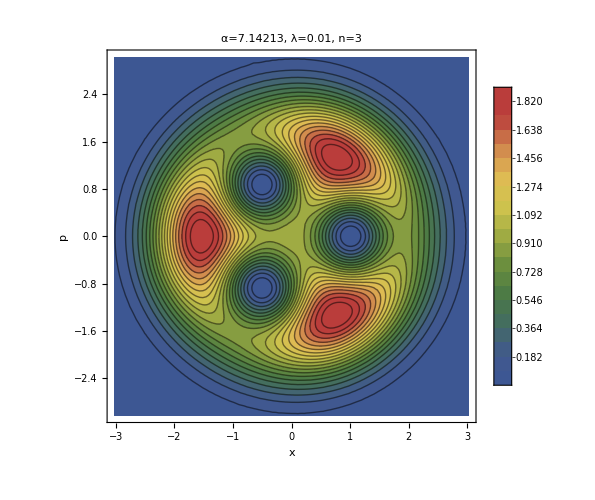

```mathematica
n=3;
λ=0.01;
γ=(n-1)/2*λ;
r0=1;
ϕ=0;
α0=r0*Exp[I*ϕ]/√(2λ);

α=α0*Exp[γ];
σ=2λ/(1-Exp[-2γ]);
HT[x_,p_,α_,n_,λ_,σ_]:=1/Abs[α]^(2n)*Exp[-n*γ]*(((x-I*p)/(√(2λ))  )^n-Conjugate[α]^n)*(((x+I*p)/(√(2λ))  )^n-α^n)*Exp[-(x^2+p^2)/σ];

r=3.0*Abs[α]*√(2λ);
ContourPlot[HT[x,p,α,n,λ,σ],{x,-r,r},{p,-r,r},PlotRange->All,Contours->20,ImageSize->500,Frame->True,FrameLabel->{Style["x",30,Bold],Style["p",30,Bold]},PlotLabel->Style["α="<>ToString[α]<>", λ="<>ToString[λ]<>", n="<>ToString[n],20],PlotLegends-> Automatic,AspectRatio->1/1,FrameStyle->Directive[Black,Thickness[0.005],30],ColorFunction->ColorData["DarkRainbow"] ]

Plot3D[HT[x,p,α,n,λ,σ],{x,-r,r},{p,-r,r},PlotRange->All,ImageSize->500,PlotLabel->Style["α="<>ToString[α]<>", λ="<>ToString[λ]<>", n="<>ToString[n],20],PlotLegends-> Automatic,AspectRatio->1/1 ]
```